```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tpdf=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],x]
```

```mathematica
fTwoDist[η_]:=PDF[BetaDistribution[η,1/2],x]
```

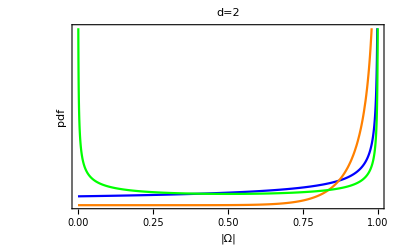

```mathematica
g1=Plot[{fTwoDist[1],fTwoDist[10],fTwoDist[0.5]},{x,0,1},PlotRange->{Full,{0,10}},PlotStyle->{Blue,Orange,Green},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->16},FrameLabel->{"|Ω|","pdf"},PlotLabel->"d=2"]
```

```mathematica
fThreePDF[η_]:=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[η,1],v\[Distributed]BetaDistribution[η+(1/2),1/2]}],x]
uPDF = fPDF[1]
hPDF = fPDF[10]
lPDF = fPDF[0.5]
```

```mathematica
uPDF=Piecewise[{{Indeterminate, x==0}, {(-(2 √x)/(√(1-x))+(2 x)/(√(-(-1+x) x))+4 ArcCos[√x])/π, 0<x<1}, {0, True}}]
```

```mathematica
hPDF=Piecewise[{{-1/(14549535 π)2 ((41287680 x^(19/2))/(√(1-x))-14549535/(2 √(-(-1+x) x))+(14549535 (1-2 x))/(2 √(-(-1+x) x))-(4849845 x^2 (-3+4 x))/(√(-(-1+x) x^3))-(3879876 x^4 (-5+6 x))/(√(-(-1+x) x^5))-(3325608 x^6 (-7+8 x))/(√(-(-1+x) x^7))-(2956096 x^8 (-9+10 x))/(√(-(-1+x) x^9))-(2687360 x^10 (-11+12 x))/(√(-(-1+x) x^11))-(2480640 x^12 (-13+14 x))/(√(-(-1+x) x^13))-(2315264 x^14 (-15+16 x))/(√(-(-1+x) x^15))-(2179072 x^16 (-17+18 x))/(√(-(-1+x) x^17))-(2064384 x^18 (-19+20 x))/(√(-(-1+x) x^19))-825753600 x^9 ArcCos[√x]), 0<x<1}, {0, True}}]
```

```mathematica
lPDF=Piecewise[{{Indeterminate, x==0}, {1/2 (-1/(√(1-x))+1./(√(1.-1. x))+ArcCos[√x]/(√x)), 0<x<1}, {0, True}}]
```

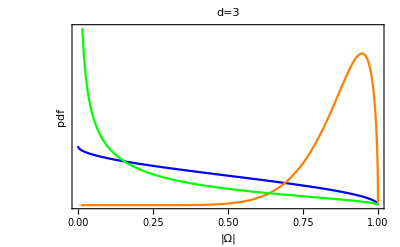

```mathematica
g2=Plot[{uPDF,hPDF,lPDF},{x,0,1},PlotRange->{Full,{0,6}},PlotStyle->{Blue,Orange,Green},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->16},FrameLabel->{"|Ω|","pdf"},PlotLabel->"d=3"]
```

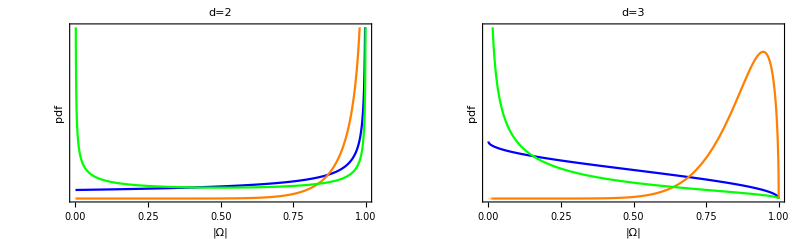

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_LKJ_determinants.pdf",gFinal]
```

Distributions_LKJ_determinants.pdf

```mathematica
threePDF = PDF[TransformedDistribution[u v w,{u\[Distributed]BetaDistribution[1,3/2],v\[Distributed]BetaDistribution[3/2,1],w\[Distributed]BetaDistribution[2,1/2]}],x]
```

$Aborted

```mathematica
fApprox[n_Integer]:=Module[{aList=RandomVariate[BetaDistribution[1,3/2],{n}],bList=RandomVariate[BetaDistribution[3/2,1],{n}],cList=RandomVariate[BetaDistribution[2,1/2],{n}]},aList bList cList]
```

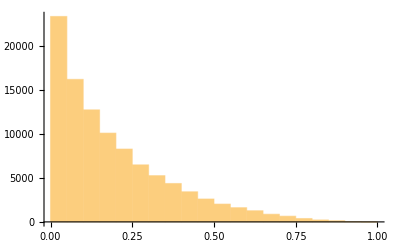

```mathematica
Histogram[fApprox[100000]]
```

```mathematica
cf=CharacteristicFunction[TransformedDistribution[u v w,{u\[Distributed]BetaDistribution[1,3/2],v\[Distributed]BetaDistribution[3/2,1],w\[Distributed]BetaDistribution[2,1/2]}],t]
```

$Aborted

```mathematica
MomentGeneratingFunction[TransformedDistribution[u v w,{u\[Distributed]BetaDistribution[1,3/2],v\[Distributed]BetaDistribution[3/2,1],w\[Distributed]BetaDistribution[2,1/2]}],I t]
```

$Aborted